```mathematica
degree=8;

polynomials=Total[Thread[{#,powers}]/.{a_?NumericQ,b_}:>{a*x^b}]&/@%;
```

```mathematica
getRoots[polynomials_]:={Re[#],Im[#]}&/@(NSolve[#==0, x]&/@polynomials/.Rule[a_,b_]:>b//Flatten)
getSelectedRoots[polynomials_]:=getRoots[polynomials]//Union
getPolRoots[degree_,alpha_]:=Total[Thread[{#,Range[0,degree-1]}]/.{a_?NumericQ,b_}:>{a*x^b}]&/@Tuples[{alpha,1},degree]
```

```mathematica
getOffsetedRoots[degree_, offset_]:=getSelectedRoots[getPolRoots[degree,offset]]/.{a_,b_?NumericQ}:>{a,b,offset}
```

```mathematica
Flatten[getSelectedRoots[getPolRoots[5,-.5]]/.{a_,b_?NumericQ}:>{a,b,5}/.{a_,b_?NumericQ}:>{a,b,5},0]
```

{{0.0367036,0.864672,5},{0.0490032,1.15443,5},{0.130841,0.78112,5},{0.208589,1.24527,5},{0.274204,0.717893,5},{0.309017,0.951057,5},{0.39192,0.619505,5},{0.464313,1.21562,5},{0.470381,0.666679,5},{0.510663,0.332475,5},{0.579156,0.815217,5},{0.609751,0.515095,5},{0.640388,0.768051,5},{0.706576,1.00144,5},{0.729306,1.15281,5},{0.780776,0.624811,5},{0.925391,0.379015,5},{0.957043,0.808476,5},{1.37528,0.895395,5}}

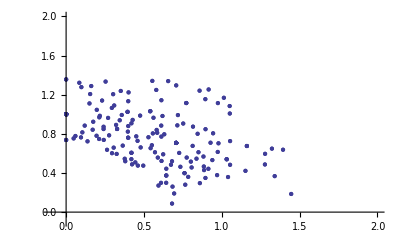

```mathematica
selectedroots=Select[roots,(#[[1]]>=0&&#[[2]]>0)&];
ListPlot[selectedroots,PlotRange->{{-0.1,2},{-0.1,2}}]
```

```mathematica
moves=Table[-(1.15^i),{i,20,1,-1}]~Join~Table[i,{i,-1,1,0.1}]~Join~Table[1.15^i,{i,1,20}]
```

{-16.3665,-14.2318,-12.3755,-10.7613,-9.35762,-8.13706,-7.07571,-6.15279,-5.35025,-4.65239,-4.04556,-3.51788,-3.05902,-2.66002,-2.31306,-2.01136,-1.74901,-1.52087,-1.3225,-1.15,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.15,1.3225,1.52087,1.74901,2.01136,2.31306,2.66002,3.05902,3.51788,4.04556,4.65239,5.35025,6.15279,7.07571,8.13706,9.35762,10.7613,12.3755,14.2318,16.3665}

```mathematica
r=Flatten[(getSelectedRoots[getPolRoots[6,#]]/.{a_,b_?NumericQ}:>{a,b,#})&/@moves,1];
```

```mathematica
r2=r[[2;;5]]
```

{{0.00157742,1.02839,-16.3665},{0.220448,0.78571,-16.3665},{0.236277,0.781661,-16.3665},{0.309017,0.951057,-16.3665}}

```mathematica
Flatten[r2,1]
```

{0.00157742,1.02839,-16.3665,0.220448,0.78571,-16.3665,0.236277,0.781661,-16.3665,0.309017,0.951057,-16.3665}

```mathematica
Length[r]
```

16464

```mathematica
theta=1
plot2=ListPointPlot3D[r,PlotRange->{{-6,6},{-4,4},{-6,6}},ViewCenter->True, ViewPoint->{-10,10*Sin[theta],-10},Axes->True,AxesOrigin->{0,0,0},Boxed->False]
```

```mathematica
ListPointPlot3D[r,PlotRange->{{-6,6},{-6,6},{-6,6}},ViewCenter->True, ViewAngle->0.2,Axes->True,AxesOrigin->{0,0,0},Boxed->False]
```

-Graphics3D-

```mathematica
axis={1,1,1};
l={-7,7};
z[x_,y_]:=Exp[-(Sqrt[x^2+y^2]/Power[4,(3)^-1])+Power[4,(3)^-1]*Sqrt[1/2*(Sqrt[x^2+y^2]+x)]];
plot=Plot3D[2*z[x,y],{x,-5,5},{y,-5,5},PlotRange->{l,l,l}];
```

```mathematica
Rotate[plot,0.4]
```

-Graphics3D-

```mathematica
s=Table[ListPointPlot3D[r,PlotRange->{{-6,6},{-6,6},{-6,6}},ViewCenter->True, ViewPoint->{15,15Sin[theta],15Cos[theta]},Axes->True,AxesOrigin->{0,0,0},Boxed->False],{theta,0.,0.5,0.01}];
```

```mathematica
Export["/home/jirka/test.gif",s, "DisplayDurations" -> 0.2]
```

/home/jirka/test.gif

```mathematica
s
Length[s]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

4

```mathematica
s[[3]]
```

-Graphics3D-